```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ExpPredfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps.csv"}],"csv"];
ExpPreyfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPrey_fit_table_revreps_large.csv"}],"csv"];
ExpPredmassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPredmass_tablereps.csv"}],"csv"];
ExpPreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPreymass_tablereps_large.csv"}],"csv"];
RawPreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/RawPreymass.csv"}],"csv"];
RawPreymassdataDelong = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/RawPreymass_delong.csv"}],"csv"];
Mammalianfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/mammalian_fit_table.csv"}],"csv"];
Mammalianmassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/mammalian_mass.csv"}],"csv"];
LogitMatrixData = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/logit_matrix_meso.csv"}],"csv"];
```

Calculate the Expected size of a predator given an herbivore consumer of size M

```mathematica
(*The Prey's perspective is captured using the bootstrapped Hayward data*)
OptPredMass[M_]:=ExpPredint*M^ExpPredslope;
ExpPredslope = (ExpPredfitdata[[3,1]]);
ExpPredint = Exp[(ExpPredfitdata[[2,1]])]*((1/1000)^ExpPredslope)*1000; (*converted from KG to grams*)

(*The Predator's perspective is captured using the combined Delong/Hayward means*)
OptPreyMass[Mp_]:=ExpPreyint*(Mp)^ExpPreyslope;
ExpPreyslope = (Mammalianfitdata[[3,1]]);
ExpPreyint = Exp[(Mammalianfitdata[[2,1]])]*((1/1000)^ExpPreyslope)*1000; (*converted from KG to grams*)

(*Integrate over KG mass values, because that is what is used in {alpha,beta,gamma} optimization*)
plink[alpha_,beta_,gamma_,M_,Mp_]:=Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]/(1+Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]);
(*ExpPreyMassLogit[logitvec_,Mp_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*M,{M,1000/1000,(10^7)/1000}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp],{M,1000/1000,(10^7)/1000}];*)

ExpPreyMassLogit[logitvec_,PreyMassVec_,Mp_]:=Sum[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],PreyMassVec[[j]],Mp]*PreyMassVec[[j]],{j,1,Length[PreyMassVec]}]/Sum[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],PreyMassVec[[j]],Mp],{j,1,Length[PreyMassVec]}];

ExpectedPredMass[logitvec_,PredMassVec_,M_]:=(∑_(j=1)^Length[PredMassVec] plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,PredMassVec[[j]]]);

(*Species-Specific Logit Vecs*)
ExpectedPredMassSpeciesSpecific[logitmatrix_,PredMassVec_,M_]:=(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],M,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],M,PredMassVec[[j]]]);
(*Complex Relationship -- doesn't work so well*)
(*ExpPredMassGenForm[logitvec_,PredMassMean_,PredMassSD_,M_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD))*Mp,{Mp,1,10^6}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD)),{Mp,1,10^6}];
PredMassMeso= {5,45,80,250,5000,12500,35000,60000,110000};
alphameso =-1.5;
betameso =-1;
gammameso =-0.12;
logitmeso = {alphameso,betameso,gammameso};
OptPredMass[M_] := Quiet[Evaluate[ExpPredMassGenForm[logitmeso,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000}),M]//Simplify]];*)
```

# Expected Prey Mass given Predator Mass

```mathematica
PredMassMacro = {93,93,108,317,36,12,1180,2.4,2633,102,6500,4,9,20,3.5,136,3.8,22,0.04,145,309,35};
macroserengetilogitvec={2.0558989052412504,-1.918476481051926,0.047825684997587214};
mesologitvec={-1.5,-1,-0.12};
LogitMatrixMeso = Transpose[{LogitMatrixData[[2;;13,2]],LogitMatrixData[[2;;13,3]],LogitMatrixData[[2;;13,4]]}]
mesogenerallogitvec = {-1.5,-1,-0.12};
mesofelidslogitvec ={-1.12,-1.38,-0.20};(* {-0.84,-0.87,-0.12};*)
mesononfelidslogitvec={-2.84,-0.67,-0.01};
(*{-2.2,-0.67,-0.02};*)
PredMassMeso = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2,23.2,9.83,5.23,6.949};
PredMassMesoSmilo = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2,23.2,9.83,5.23,6.949,220};
PredMassMesoFelids = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2}; (*Smilodon populator=338 (220, 436)*)
PredMassMesoNonFelids = {23.2,9.83,5.23,6.949};
```

{{-2.63935,-3.08932,-0.493212},{-1.13229,-1.28659,-0.225007},{-0.904094,-1.61149,-0.201734},{-2.78341,-1.31059,-0.128346},{-0.179215,-1.18314,-0.220345},{-0.932505,-2.03602,-0.283136},{-0.273401,-1.14947,-0.207688},{-4.50169,-3.11868,-0.39284},{-2.80576,-1.04896,-0.0535284},{-1.54748,-0.989647,-0.112394},{-4.37324,-0.46665,0.0848872},{-5.66363,-0.265945,0.161473}}

```mathematica
(*(Add Smilodon ???)*)
```

Add Smilodon?
Option 1: Same logitvec as P. onca {-2.6,-3.1,-0.49}
Option 2: Serengetic logitvec
Option 3: Artificial logitvec... one that increases its prey size range and mean prey size might be {1, -2.45, -1}
Option 3: Artificial logitvec... If it is mainly eating things much much larger than itself, then {1, 2, -1}

```mathematica
LogitMatrixMesoSmilo = Append[LogitMatrixMeso,{1,-2,-1}];
```

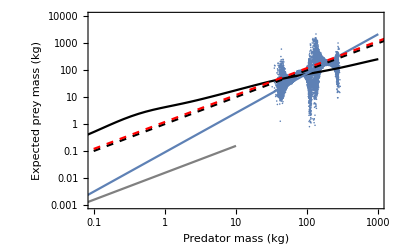

```mathematica
Show[{
ListLogLogPlot[ExpPreymassdata,Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,1000},{1/1000,(10^7)/1000}}],
LogLogPlot[ExpPreyMassLogit[macroserengetilogitvec,PredMassMacro,Mp],{Mp,10/1000,(10^6)/1000},PlotStyle->Black],
LogLogPlot[OptPreyMass[Mp]/1000/.Mp->(Mpkg*1000),{Mpkg,(10^1)/1000,(10^6)/1000}],
LogLogPlot[Mp*Exp[-mesologitvec[[2]]/(2*mesologitvec[[3]])],{Mp,(10^1)/1000,10},PlotStyle->Gray],
LogLogPlot[Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Black, Dashed}]], (*1:1*)
LogLogPlot[1.19*Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Red, Dashed}]] (*Carbone 2001*)
}]
```

Fit raw values from Hayward with values from Delong’s Forage database

```mathematica
poslarge = Flatten[Position[RawPreymassdata[[All,1]],_?(#>50&)],1]
```

{1,2,3,6,7}

```mathematica
RawPreymassdatalarge=RawPreymassdata[[poslarge]]
```

{{204.,143.995},{79.5,125.168},{81.5,39.0647},{63.5,36.3205},{195.,223.278}}

```mathematica
lm =LinearModelFit[Log@(RawPreymassdatalarge),x,x];
lmparams=lm["BestFitParameters"];
```

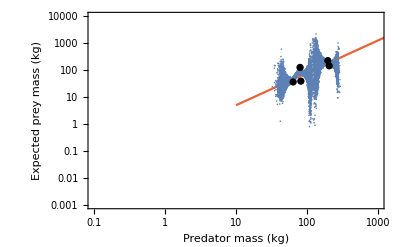

```mathematica
RawPreyFit = Show[{
ListLogLogPlot[(RawPreymassdatalarge),Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,1000},{1/1000,(10^7)/1000}}],
LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,10^7},PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPreymassdata,Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,1000},{1/1000,(10^7)/1000}}],
ListLogLogPlot[(RawPreymassdatalarge),PlotStyle->Black]
}]
```

```mathematica
lmparams
```

{-1.16914,1.20378}

```mathematica
RawPreymassdatalarge
```

{{204.,143.995},{79.5,125.168},{81.5,39.0647},{63.5,36.3205},{195.,223.278}}

```mathematica
lmAll =LinearModelFit[Log@(RawPreymassdata),x,x];
lmparamsAll=lmAll["BestFitParameters"]
```

{2.21525,0.503957}

Combine with Delong Data

```mathematica
Mammalianfitdata
```

{{Fit,FitLow,FitHigh},{-2.41385,-3.75293,-1.07477},{1.45999,1.09945,1.82053}}

```mathematica
Mammalianfitdata[[3,1]]
```

1.45999

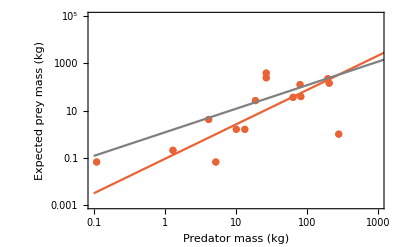

```mathematica
(*MammalianMeanMassData=Join[RawPreymassdata,RawPreymassdataDelong];*)
mammalianint=Mammalianfitdata[[2,1]];
mammalianslope =Mammalianfitdata[[3,1]];
(*mammalianlm =LinearModelFit[Log@(MammalianMeanMassData),x,x];
mammalianlmparams=mammalianlm["BestFitParameters"];*)
PreyPerspectivePlot = Show[{
ListLogLogPlot[(Mammalianmassdata),Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,10^3},{1/1000,(10^8)/1000}},PlotStyle->ColorData[97,4],LabelStyle->Directive[FontSize->16]],
LogLogPlot[Exp[mammalianint]*x^(mammalianslope),{x,10^-1,10^7},PlotStyle->ColorData[97,4]],
(*ListLogLogPlot[ExpPreymassdata,Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,1000},{1/1000,(10^7)/1000}}],*)
ListLogLogPlot[(Mammalianmassdata),PlotStyle->ColorData[97,4]],
LogLogPlot[1.19*Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Gray}]] (*Carbone 1999*)(*,
LogLogPlot[Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Dashed,Black}]] *)
(*LogLogPlot[ExpPreyMassLogit[macroserengetilogitvec,PredMassMacro,Mp],{Mp,10/1000,(10^6)/1000},PlotStyle->Black]*)
(*LogLogPlot[OptPreyMass[Mp]/1000/.Mp->(Mpkg*1000),{Mpkg,(10^1)/1000,(10^6)/1000}]*)(*,
LogLogPlot[Mp*Exp[-mesologitvec[[2]]/(2*mesologitvec[[3]])],{Mp,(10^1)/1000,10},PlotStyle->Gray]*)
}]
```

```mathematica
{mammalianslope,mammalianint}
```

{1.45999,-2.41385}

# Expected Predator Mass given Prey Mass

```mathematica
(*ExpectedPredMassMeanMeso[M_] := Mean[{ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M]}];*)
(*Weighted average by length of Felid/NonFelid categories*)
ExpectedPredMassMeanMeso[M_] := (Length[PredMassMesoFelids]/Length[PredMassMeso])*ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M]+(Length[PredMassMesoNonFelids]/Length[PredMassMeso])*ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M];
```

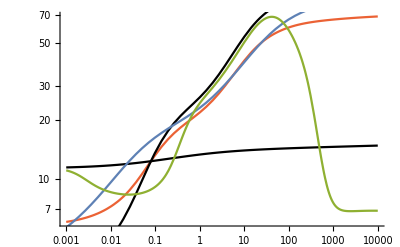

```mathematica
Show[{
LogLogPlot[ExpectedPredMassMeanMeso[M],{M,10^-3,10^4},PlotStyle->ColorData[97,4]],
LogLogPlot[ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesogenerallogitvec,PredMassMeso,M],{M,10^-3,10^4},PlotStyle->ColorData[97,1]],
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso,PredMassMeso,M],{M,10^-3,10^4},PlotStyle->ColorData[97,3]]
}]
```

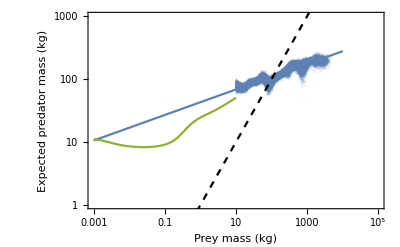

```mathematica
PredPerspectivePlot=Show[{
ListLogLogPlot[ExpPredmassdata,Frame->True,FrameLabel->{"Prey mass (kg)","Expected predator mass (kg)"},PlotRange->{{10^-3,10^5},{10^0,10^3}},PlotStyle->Directive[{Opacity[0.1],ColorData[97,1]}],LabelStyle->Directive[FontSize->16]],
LogLogPlot[OptPredMass[M]/1000/.M->Mkg*1000,{Mkg,10^-3,10^4},PlotStyle->ColorData[97,1]],
(*LogLogPlot[ExpectedPredMassMeanMeso[M],{M,10^-3,10^4},PlotStyle->Black],*)
(*LogLogPlot[ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M],{M,10^-3,10^4},PlotStyle->Black],*)
(*LogLogPlot[ExpectedPredMass[mesogenerallogitvec,PredMassMeso,M],{M,10^-3,200},PlotStyle->ColorData[97,1]],*)
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso,PredMassMeso,M],{M,10^-3,10^1},PlotStyle->ColorData[97,3]],
(*LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMesoSmilo,PredMassMesoSmilo,M],{M,10^-3,200},PlotStyle->Directive[{ColorData[97,4],Dashed}]],*)

(*Felids*)
(*LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso[[1;;8,All]],PredMassMeso[[1;;8]],M],{M,10^-3,100},PlotStyle->Directive[{ColorData[97,5]}]],*)
(*NonFelids*)
(*LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso[[9;;12,All]],PredMassMeso[[9;;12]],M],{M,10^-3,20},PlotStyle->Directive[{ColorData[97,5]}]],*)
(*ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMeso],
ListLogLogPlot[MeanMesoNonFelidsFelids,PlotStyle->ColorData[97,5]],*)
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[M,{M,10^-3,10^4},PlotStyle->Directive[{Black,Dashed}]]
}]
```

```mathematica
Min[ExpPredmassdata[[All,2]]]
```

48.7622

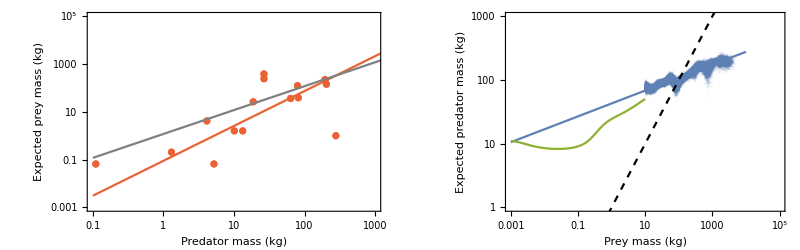

```mathematica
PerspectivesPlot=GraphicsRow[{PreyPerspectivePlot,PredPerspectivePlot},ImageSize->800]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_perspectives.png"}],PerspectivesPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_perspectives.png

Are there size ranges where E{Mc} is more similar/different than E{Mp}?

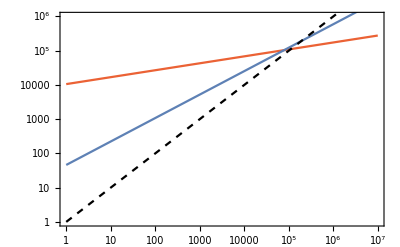

```mathematica
Show[{
LogLogPlot[OptPredMass[M],{M,1,10^7},PlotStyle->ColorData[97,4],Frame->True,PlotRange->{1,10^6}],
LogLogPlot[(M/ExpPreyint)^(1/ExpPreyslope),{M,1,10^7}],
LogLogPlot[M,{M,1,10^7},PlotStyle->{Dashed,Black}]
}]
```

```mathematica
OptPredMass[M]
```

10574.4 M^0.202659

```mathematica
OptPreyMass[Mp]
```

0.00372996 Mp^1.45999

```mathematica
(M/ExpPreyint)^(1/ExpPreyslope)
```

46.0496 M^0.684936

```mathematica
ExpPreyint
ExpPreyslope
```

0.00372996

1.45999